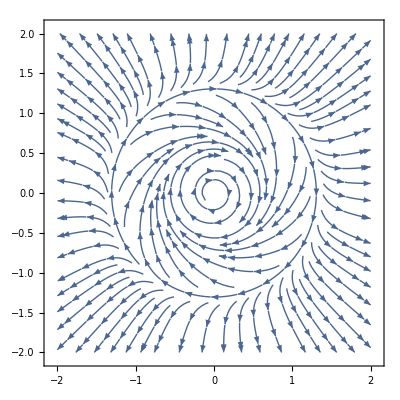

```mathematica
(* 1 Plot for μ=0.5 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+0.5)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}]
```

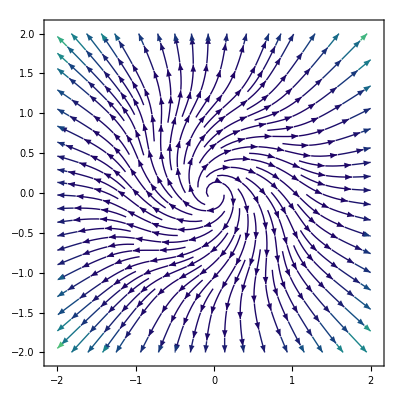

```mathematica
(* 1 Plot for μ=2 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+2)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamColorFunction->"BlueGreenYellow"]
```

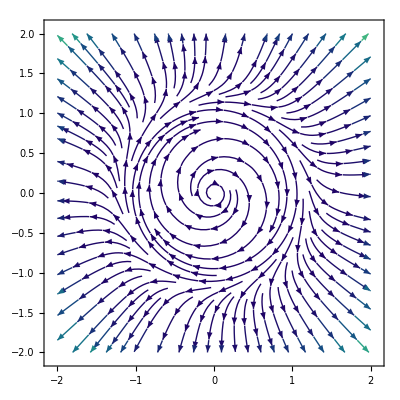

```mathematica
(* 1 Plot for μ=2 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{(r^4-2*r^2+1)*r,-1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamColorFunction->"BlueGreenYellow"]
```

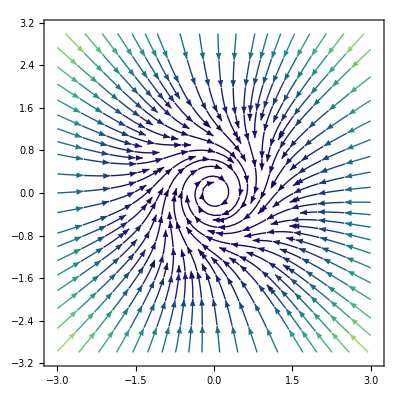

```mathematica
(* 2 Plot for μ=0.5 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.5*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

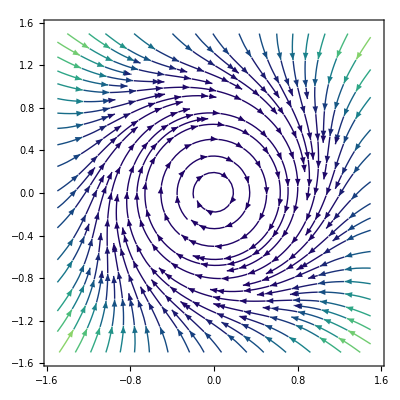

```mathematica
(* 2 Plot for μ=0.25 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.25*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1.5,3/2},{y,-3/2,3/2},StreamColorFunction->"BlueGreenYellow"]
```

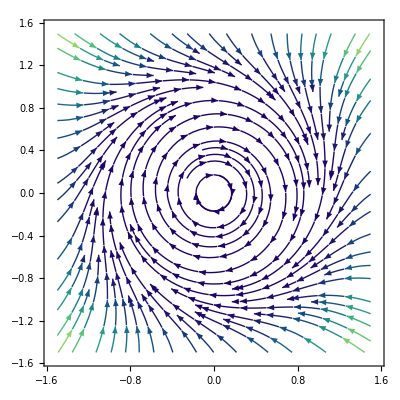

```mathematica
(* 2 Plot for μ=0.125 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.125*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1.5,3/2},{y,-3/2,3/2},StreamColorFunction->"BlueGreenYellow"]
```

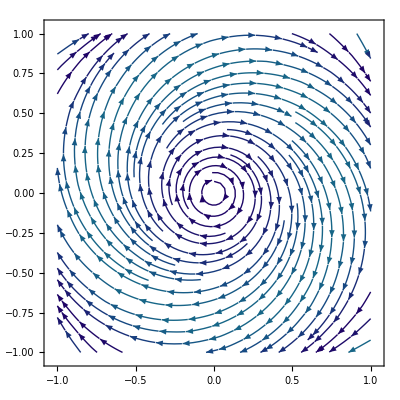

```mathematica
(* 2 Plot for μ=-0.25 *)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{0.25*r+r^2-r^3,-1},{r,θ}->{x,y}],{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

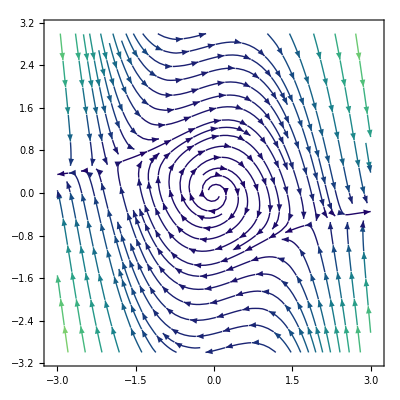

```mathematica
(* 3a Plot for μ=0.25 *)
StreamPlot[{y+0.25*x,-x+0.25*y-x^2*y},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

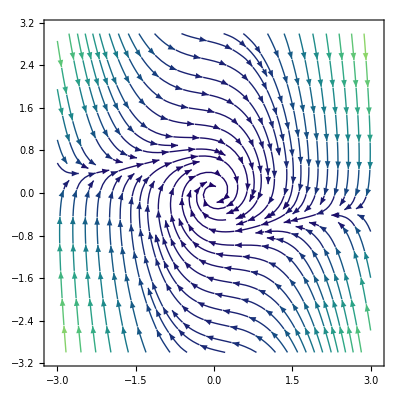

```mathematica
(* 3a Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x,-x-0.25*y-x^2*y},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
(* Hence 3a is a Supercritical Hopf Bifurcation *)
```

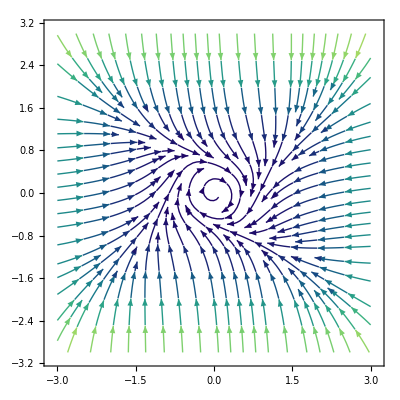

```mathematica
(* 3b Plot for μ=0.25 *)
StreamPlot[{y+0.25*x-x^3,-x+0.25*y-2*y^3},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

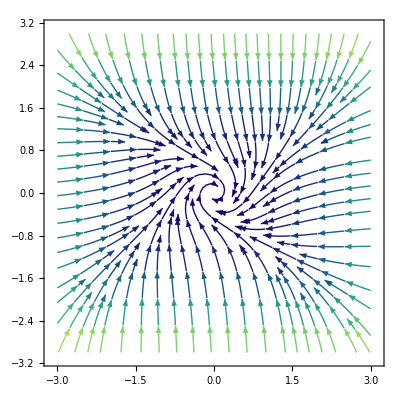

```mathematica
(* 3b Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x-x^3,-x-0.25*y-2*y^3},{x,-3,3},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
(* Hence 3b is a Supercritical Hopf Bifurcation *)
```

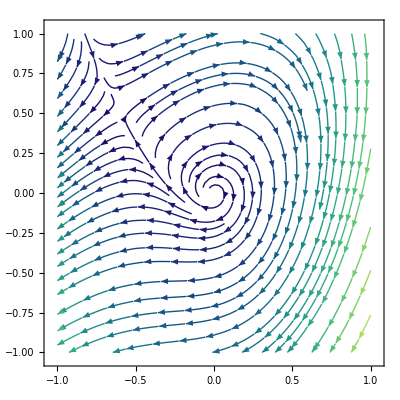

```mathematica
(* 3c Plot for μ=0.25 *)
StreamPlot[{y+0.25*x-x^2,-x+0.25*y-2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

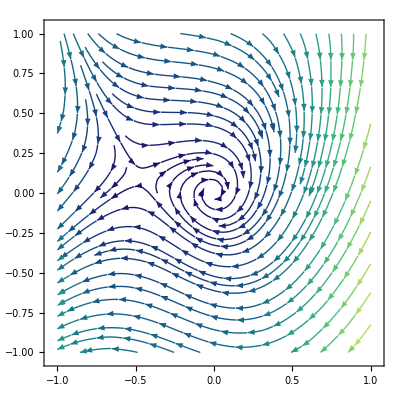

```mathematica
(* 3c Plot for μ=-0.25 *)
StreamPlot[{y-0.25*x-x^2,-x-0.25*y-2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->"BlueGreenYellow"]
```

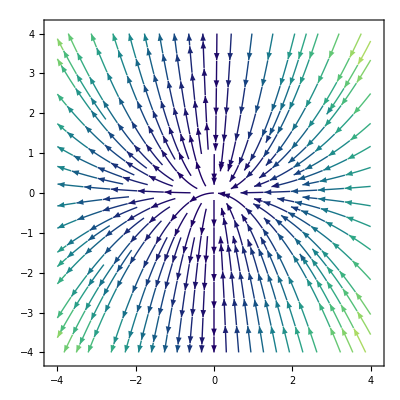

```mathematica
(* Hence 3c is a Subcritical Hopf Bifurcation *)

(* For Assignment 7 Problem 2 *)

(* μ= 0 *)

StreamPlot[{-x^2,y*(-2*x)},{x,-4,4},{y,-4,4},StreamColorFunction->"BlueGreenYellow"]
```

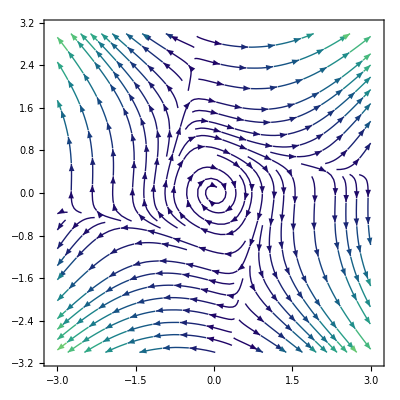

```mathematica
(* Ensem 5.1 for μ=-.25 *)
StreamPlot[{y + x*y^2,-x-0.25*y+y*x^2},{x,-3,3},{y,-3,3},
StreamColorFunction->"BlueGreenYellow"]
```

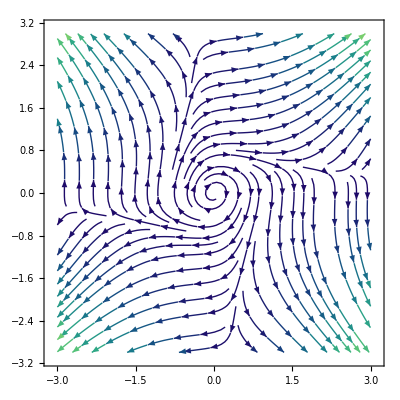

```mathematica
(* Ensem 5.1 for μ=+.25 *)
StreamPlot[{y + x*y^2,-x+0.25*y+y*x^2},{x,-3,3},{y,-3,3},
StreamColorFunction->"BlueGreenYellow"]
```

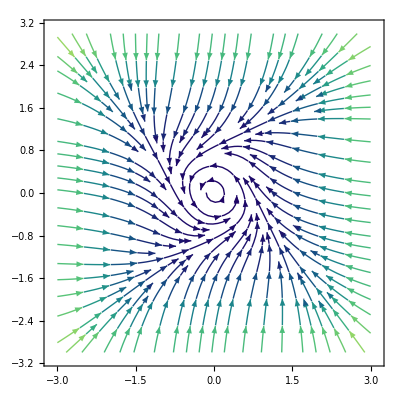

```mathematica
(* Ensem 5.2 for μ=+.25 *)
StreamPlot[{-y - x^3,x+0.25*y-y^3},{x,-3,3},{y,-3,3},
StreamColorFunction->"BlueGreenYellow"]
```

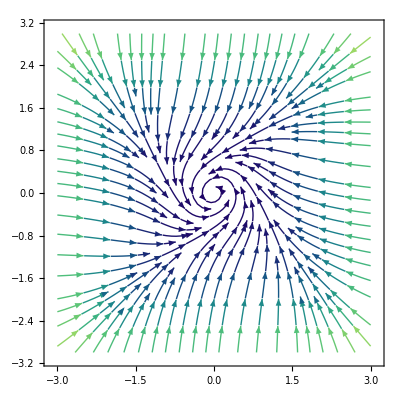

```mathematica
(* Ensem 5.2 for μ=-.25 *)
StreamPlot[{-y - x^3,x-0.25*y-y^3},{x,-3,3},{y,-3,3},
StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
Solve[-x^3+d*x+c==0,x][1]
```

{{x→-((2/3)^(1/3) d)/((-9 c+√3 √(27 c^2-4 d^3))^(1/3))-((-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))+((1-ⅈ √3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))+((1+ⅈ √3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}[1]

```mathematica
Plot3D[{-((2/3)^(1/3) d)/((-9 c+√3 √(27 c^2-4 d^3))^(1/3))-((-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2^(1/3) 3^(2/3)), ((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))+((1-ⅈ √3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3)), ((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))+((1+ⅈ √3) (-9 c+√3 √(27 c^2-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{c,-20,10},{d,-10,10}]
```

-Graphics3D-

```mathematica
Solve[-x^3+d*x+5==0,x]
```

{{x→-((2/3)^(1/3) d)/((-45+√3 √(675-4 d^3))^(1/3))-((-45+√3 √(675-4 d^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (-45+√3 √(675-4 d^3))^(1/3))+((1-ⅈ √3) (-45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (-45+√3 √(675-4 d^3))^(1/3))+((1+ⅈ √3) (-45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

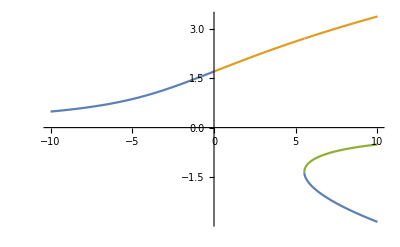

```mathematica
Plot[{-((2/3)^(1/3) d)/((-45+√3 √(675-4 d^3))^(1/3))-((-45+√3 √(675-4 d^3))^(1/3))/(2^(1/3) 3^(2/3)), ((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (-45+√3 √(675-4 d^3))^(1/3))+((1-ⅈ √3) (-45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3)), ((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (-45+√3 √(675-4 d^3))^(1/3))+((1+ⅈ √3) (-45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{d,-10,10}]
```

```mathematica
Solve[-x^3+d*x-5==0,x]
```

{{x→-((2/3)^(1/3) d)/((45+√3 √(675-4 d^3))^(1/3))-((45+√3 √(675-4 d^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (45+√3 √(675-4 d^3))^(1/3))+((1-ⅈ √3) (45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (45+√3 √(675-4 d^3))^(1/3))+((1+ⅈ √3) (45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

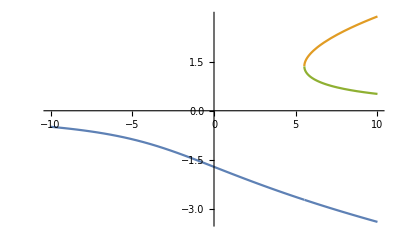

```mathematica
Plot[{-((2/3)^(1/3) d)/((45+√3 √(675-4 d^3))^(1/3))-((45+√3 √(675-4 d^3))^(1/3))/(2^(1/3) 3^(2/3)),((1+ⅈ √3) d)/(2^(2/3) 3^(1/3) (45+√3 √(675-4 d^3))^(1/3))+((1-ⅈ √3) (45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3)),((1-ⅈ √3) d)/(2^(2/3) 3^(1/3) (45+√3 √(675-4 d^3))^(1/3))+((1+ⅈ √3) (45+√3 √(675-4 d^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{d,-10,10}]
```

```mathematica
Solve[-x^3+5*x+c==0,x]
```

{{x→-(5 (2/3)^(1/3))/((-9 c+√3 √(-500+27 c^2))^(1/3))-((-9 c+√3 √(-500+27 c^2))^(1/3))/(2^(1/3) 3^(2/3))},{x→(5 (1+ⅈ √3))/(2^(2/3) 3^(1/3) (-9 c+√3 √(-500+27 c^2))^(1/3))+((1-ⅈ √3) (-9 c+√3 √(-500+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→(5 (1-ⅈ √3))/(2^(2/3) 3^(1/3) (-9 c+√3 √(-500+27 c^2))^(1/3))+((1+ⅈ √3) (-9 c+√3 √(-500+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))}}

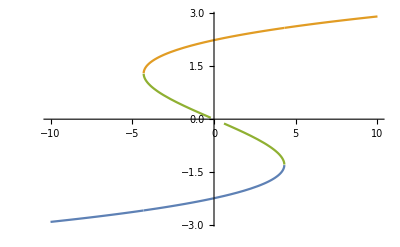

```mathematica
Plot[{-(5 (2/3)^(1/3))/((-9 c+√3 √(-500+27 c^2))^(1/3))-((-9 c+√3 √(-500+27 c^2))^(1/3))/(2^(1/3) 3^(2/3)),(5 (1+ⅈ √3))/(2^(2/3) 3^(1/3) (-9 c+√3 √(-500+27 c^2))^(1/3))+((1-ⅈ √3) (-9 c+√3 √(-500+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3)),(5 (1-ⅈ √3))/(2^(2/3) 3^(1/3) (-9 c+√3 √(-500+27 c^2))^(1/3))+((1+ⅈ √3) (-9 c+√3 √(-500+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))},{c,-10,10}]
```

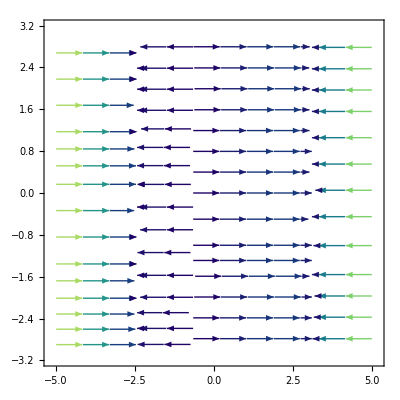

```mathematica
StreamPlot[{-x^3+8*x+5, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

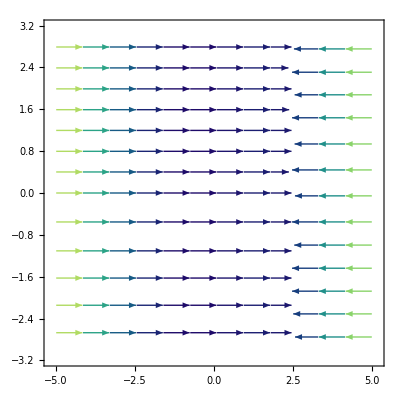

```mathematica
StreamPlot[{-x^3+4*x+5, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

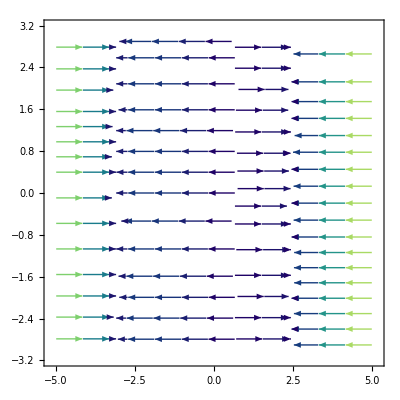

```mathematica
StreamPlot[{-x^3+8*x-5, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

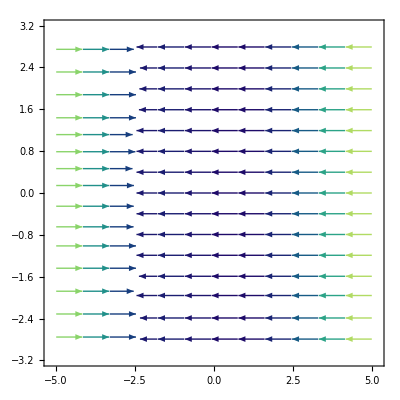

```mathematica
StreamPlot[{-x^3+4*x-5, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
Solve[-x^3+d*x==0,x]
```

{{x→0},{x→-√d},{x→√d}}

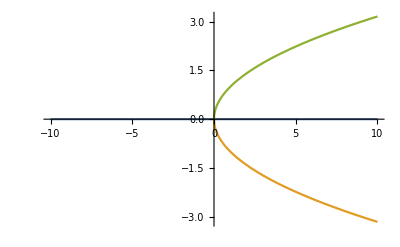

```mathematica
Plot[{0, -√d, √d},{d,-10,10}]
```

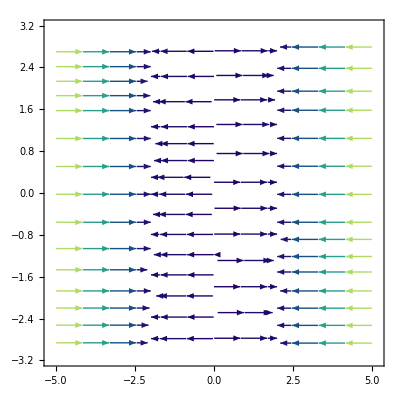

```mathematica
StreamPlot[{-x^3+4*x, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

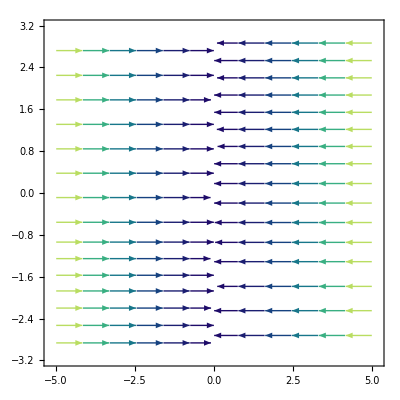

```mathematica
StreamPlot[{-x^3-4*x, 0},{x,-5,5},{y,-3,3},StreamColorFunction->"BlueGreenYellow"]
```

```mathematica
e
```

e

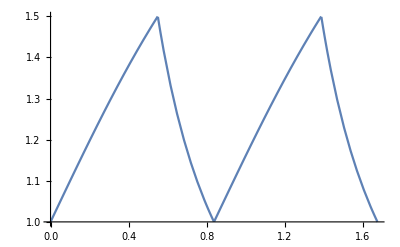

```mathematica
Plot[Piecewise[{{(2. ⅇ^(2. x))/(1.+ⅇ^(2. x)),0<x<Log[3^0.5]},
{(0.5 ⅇ^x)/((-1.1547005383792517+0. ⅈ)+ⅇ^x),Log[3^0.5]<x<Log[4/(3^0.5)]},
{-(2. ⅇ^(2. x))/(-5.333333333333335-1. ⅇ^(2. x)),Log[4/(3^0.5)]<x<Log[4/(3^0.5)]+Log[3^0.5]},
{(0.5 ⅇ^x)/((-2.666666666666667+0. ⅈ)+ⅇ^x),
Log[4/(3^0.5)]+Log[3^0.5]<x<Log[4/(3^0.5)]+Log[4/(3^0.5)]}}],{x,0,2*Log[4/(3^0.5)]}]
```

```mathematica
Solve[x == Log[4/(3^0.5)]+0.5 * Log[y/(2-y)], y]
```

{{y→-(2. ⅇ^(2. x))/(-5.33333-1. ⅇ^(2. x))}}

```mathematica
Solve[x == Log[4/(3^0.5)]+ 0.5*Log[3] + Log[4*y/(3*(2*y-1))], y]
```

{{y→(0.5 ⅇ^x)/((-2.66667+0. ⅈ)+ⅇ^x)}}

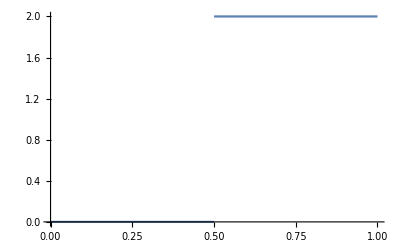

```mathematica
Plot[Piecewise[{{0,0<x<0.5},
{2,0.5<x<1}}],{x,0,1}]
```

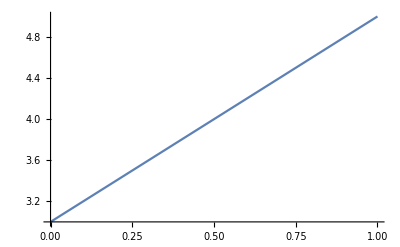

```mathematica
Plot[3+2*x,{x,0,1}]
```